# Amplitude Pulse-Shaping Last Updated: 5/24/2021

```mathematica
Quit[]
```

```mathematica
Remove["Global`*"];ClearInOut[];
```

## 0 Prep

## 0.0 Setup

### 0.0.1 User Config

```mathematica
(*user input*)
	(*enter chain configuration*)
(*mArr={mMol,mMol};*)
```

```mathematica
mArr={mMol,mMol,mMol,mMol,mAtom};
```

### 0.0.2 Config - RDX

```mathematica
(*qubits*)
numIons=Length[mArr];
```

```mathematica
(*ion positions*)
indMol:=Position[mArr,mMol]//Flatten;
indAtom:=Position[mArr,mAtom]//Flatten;
```

### 0.0.3 Useful Functions

```mathematica
Off[General::munfl];
```

```mathematica
(*play sound when finished*)
Done[type_:"none",msg_:""]:=With[{soundDJ=Play[Sin[600*π*t],{t,0,0.6}],message="Calc Done"},
Switch[type,
"text",SendMessage["SMS",message],
"email",SendMail[<|"To"->"claytonho@g.ucla.edu","Subject"->"Calc Done: "<>ToString[msg],"From"->"claytonho@physics.ucla.edu","Server"->"smtp.physics.ucla.edu","EncryptionProtocol"->"SSL","PortNumber"->465,"UserName"->"claytonho@physics.ucla.edu","Password"->"I2Ic1zIS2R"|>],
"none",EmitSound[soundDJ]];];
```

## 0.1 Values

### 0.1.1 Constants

```mathematica
(*fundamental*)
ℏ=1.0545718*^-34;me=9.10938356*^-31;qe=1.60217662*^-19;c=2.99792458*^8;kb=1.38064852*^-23;
```

```mathematica
(*derived*)
ke2=2.30707751*^-28;a0=ℏ^2/me/ke2;
```

```mathematica
(*defined*)
amu=1.66053904*^-27;wghz=2π 1.*^9;wmhz=2π 1.*^6;wkhz=2π 1.*^3;debye=1.*^-21/c;μs=1.*^-6;mm=1.*^-3;nm=1.*^-9;
```

### 0.1.2 Variables

```mathematica
(*mMol=38*amu;mAtom=40*amu;*)
```

```mathematica
mMol=171*amu;mAtom=138*amu;
Δk=N[2*^9*2π/(mArr/.{mMol->355,mAtom->532})];
```

### 0.1.3 Quick Eigen

#### 0.2.3.1 in terms of ω_(sec-Mol), fixed ω_sec

```mathematica
wsecMol={3.06,0.16}*wmhz;
wsecAtom:={Sqrt[((wsecMol[[1]])^2+0.5*(#)^2)*(mMol/mAtom)^2-0.5*(#)^2*mMol/mAtom],#*Sqrt[mMol/mAtom]}&[wsecMol[[2]]];
```

#### 0.2.3.2 in terms of trap parameters

```mathematica
(*VRF=150;ωRF=20*wmhz;κr=1;r0=0.55*mm;
z0=2.2*mm;κz=0.06;
U=84;
qMol:=(2*qe*(VRF*κr))/(mMol*ωRF^2*r0^2);qAtom:=(2*qe*(VRF*κr))/(mAtom*ωRF^2*r0^2);
wsecMol:=ωRF/2*Sqrt[{qMol^2/2-#,2.*#}]&[(4*qe*U*κz)/(z0^2*mMol*ωRF^2)];wsecAtom:=ωRF/2*Sqrt[{qAtom^2/2-#,2.*#}]&[(4*qe*U*κz)/(z0^2*mAtom*ωRF^2)];
wsecMol/wmhz*)
```

#### 0.2.3.3 find eigen

```mathematica
(*get individual secular frequencies*)
wsecvalsMAT=Transpose[mArr/.{mMol->wsecMol}/.{mAtom->wsecAtom}];
```

```mathematica
(*Calculate equilibrium positions (axial crystal)*)
z0eqArr = Array[z0eq,numIons];l0:=(ke2/(mMol*wsecMol[[2]]^2))^(1/3);
L0EQlist=z0eqArr[[#]]==(Sum[(z0eqArr[[#]] - z0eqArr[[k]])^(-2),{k,1,#-1}] - Sum[(z0eqArr[[#]] - z0eqArr[[k]])^(-2),{k, #+1,numIons}])&/@Range[numIons];
guessz0eq=Range[-#,#,2*#/(numIons-1)]&[numIons^(1/3)]//N;guessz0eq=Transpose[Join[{z0eqArr},{guessz0eq}]];
z0eqArr=z0eqArr/.Chop[FindRoot[L0EQlist,guessz0eq]];
L0Mn=Abs[Table[If[i==j,0,(z0eqArr[[i]]-z0eqArr[[j]])^(-3)],{i,numIons},{j,numIons}]];
```

```mathematica
(*Create matrices*)
VMatZ=Table[Sqrt[mArr[[i]]/mArr[[j]]]*wsecvalsMAT[[2,i]]^2*If[i==j,1+2*Sum[L0Mn[[i,id]],{id,numIons}],-2*L0Mn[[i,j]]],{i,numIons},{j,numIons}];
VMatX=Table[Sqrt[mArr[[i]]/mArr[[j]]]*wsecvalsMAT[[2,i]]^2*If[i==j,(wsecvalsMAT[[1,i]]/wsecvalsMAT[[2,i]])^2-Sum[L0Mn[[i,id]],{id,numIons}],L0Mn[[i,j]]],{i,numIons},{j,numIons}];
(*get eigen*)
eigenholder={Eigensystem[VMatX],Eigensystem[VMatZ]};
wmvals=Sqrt[eigenholder[[;;,1]]];vmvals:=eigenholder[[;;,2]];
{vmvals[[#1]]//MatrixForm,wmvals[[#1]]/wmhz//MatrixForm}&[1]
```

{(0.000139932 | 0.00035352 | 0.00113059 | 0.00723175 | 0.999973
-0.631341 | -0.547561 | -0.450906 | -0.313465 | 0.00305869
0.679189 | -0.0741916 | -0.475781 | -0.553904 | 0.00447492
-0.35765 | 0.6745 | 0.122543 | -0.634115 | 0.00425892
0.110439 | -0.489615 | 0.745183 | -0.439063 | 0.0024904),(3.78578
3.05884
3.05216
3.04352
3.03399)}

```mathematica
wmvals[[2]]/wmhz
```

{0.588213,0.494982,0.399427,0.288458,0.163006}

```mathematica
wmvals={{3.403,3.062,3.056,3.048,3.039},{0.57,0.48,0.387,0.279,0.158}}*wmhz;
```

#### 0.2.3.4 Lamb-Dicke

```mathematica
η=√(ℏ/2.)Table[Δk[[i]]/(√(mArr[[i]]*wmvals[[d,q]]))*vmvals[[d,q,i]],{d,2},{i,numIons},{q,numIons}];
```

## 1 Calc

## 1.1 Setup

### 1.1.1 Pulse Shape

```mathematica
numPulses=5;pulseTime=200*μs;
```

```mathematica
pulseVec=Array[Ω,numPulses];
tArr=Range[0,pulseTime,pulseTime/numPulses];
```

### 1.1.2 Spin-Motion Functions

```mathematica
Aim[u_Real,ion_Integer,mode_Integer,dir_Integer]:=With[{w=wmvals[[dir,mode]]},
((ⅈ*η[[dir,ion,mode]])/(u^2-w^2))*((#1[[2;;]]-#1[[;;-2]])&[Exp[ⅈ*w*tArr]*(u*Sin[u*tArr]+ⅈ*w*Cos[u*tArr])])]
```

```mathematica
Bkl[u_,temp_,ions_,dir_]:=With[{AimMat={{Aim[u,ions[[1]],#,dir]},{Aim[u,ions[[2]],#,dir]}}&/@Range[numIons]},
1/4*(βk[temp,dir]).Apply[Plus,Map[ConjugateTranspose[#].#&,AimMat,{2}],1]]
```

```mathematica
Aim[uDJ,1,1,1]
```

{-3.18183×10^-13-6.51039×10^-13 ⅈ,-4.40698×10^-13-1.01869×10^-12 ⅈ,-2.26743×10^-13-7.60661×10^-13 ⅈ,-6.08119×10^-13-2.56775×10^-13 ⅈ,-1.03162×10^-12-3.7265×10^-13 ⅈ}

```mathematica
Integrate[Sin[u*t]*Exp[ⅈ*w*t],t]//FullSimplify;
%/.{t->1}
ⅈ*Exp[ⅈ*w*t]/(u^2-w^2)*(w*Sin[u*t]+ⅈ*u*Cos[u*t])/.{t->1}
```

(ⅇ^(ⅈ w) (u Cos[u]-ⅈ w Sin[u]))/(-u^2+w^2)

(ⅈ ⅇ^(ⅈ w) (ⅈ u Cos[u]+w Sin[u]))/(u^2-w^2)

### 1.1.3 Entanglement Functions

```mathematica
XklInd[u_,mode_,dir_]:=Module[{UpperFunc1,UpperFunc2,upper1,upper2,DiagFunc,diag,upper,w=wmvals[[dir,mode]]},
UpperFunc1[t_]:=(u^2-w^2)^-1*(u*Sin[u*t]*Cos[w*t]-w*Sin[w*t]*Cos[u*t]);upper1=(#[[2;;]]-#[[;;-2]])&[UpperFunc1/@tArr];
UpperFunc2[t_]:=(u^2-w^2)^-1*(w*Cos[w*t]*Cos[u*t]+u*Sin[w*t]*Sin[u*t]);upper2=(#[[2;;]]-#[[;;-2]])&[UpperFunc2/@tArr];
DiagFunc[a_,b_]:=-1/(u^2-w^2)(w/2((b-a)+(Sin[2*u*b]-Sin[2*u*a])/(2*u))+(u*Sin[u*a])/(u^2-w^2)(w*Cos[w*(b-a)]*Cos[u*b]+u*Sin[u*b]*Sin[w*(b-a)]-w*Cos[u*a])-(w*Cos[u*a])/(u^2-w^2)*(u*Cos[w*(b-a)]*Sin[u*b]-w*Sin[w*(b-a)]*Cos[u*b]-u*Sin[u*a]));
upper=LowerTriangularize[Transpose[#]-#]&[KroneckerProduct[upper1,upper2]];
diag=DiagonalMatrix[DiagFunc[tArr[[#]],tArr[[#+1]]]&/@Range[numPulses]];
diag+upper];
```

```mathematica
Xkl[u_,ions_List,dir_Integer]:=(Times@@η[[dir,ions,Range[numIons]]]).(XklInd[u,#,dir]&/@Range[numIons]);
```

### 1.1.4 Fidelity

```mathematica
(*phonon number*)
(*βk[temp_,dir_]:=Cosh[(ℏ*wmvals[[dir]])/(2*kb*temp)];*)
βk[temp_,dir_]:=Coth[(ℏ*wmvals[[dir]])/(2*kb*temp)];
```

```mathematica
(*for fidelity*)
Gi[u_,temp_,vec_,ion_,dir_]:=Exp[((-βk[temp,dir])/2).Abs[((Aim[u,ion,#,dir]&/@Range[numIons]).vec)]^2]
Gp[u_,temp_,vec_,ions_,dir_]:=Exp[((-βk[temp,dir])/2).Abs[(((Aim[u,ions[[1]],#,dir]+Aim[u,ions[[2]],#,dir])&/@Range[numIons]).vec)]^2]
Gm[u_,temp_,vec_,ions_,dir_]:=Exp[((-βk[temp,dir])/2).Abs[(((Aim[u,ions[[1]],#,dir]-Aim[u,ions[[2]],#,dir])&/@Range[numIons]).vec)]^2]
```

```mathematica
(*actual fidelity*)
Fid[u_,temp_,vec_,ions_,dir_]:=1/8*(2+2*(Gi[u,temp,vec,ions[[1]],dir]+Gi[u,temp,vec,ions[[2]],dir])+(Gp[u,temp,vec,ions,dir]+Gm[u,temp,vec,ions,dir]));
```

## 1.2 Generalized Eigenvalue Problem

```mathematica
(*set values du jour*)
ionsDJ={1,5};dirDJ=1;uDJ=wmvals[[1,2]]-8.*wkhz;tempDJ=5*^-4;
```

### 1.2.1 Optimize Fidelity

```mathematica
(*hold values for efficiency*)
XklDJ=Xkl[uDJ,ionsDJ,dirDJ];
BklDJ=Bkl[uDJ,tempDJ,ionsDJ,dirDJ];
```

```mathematica
(*create matrices*)
DMat=#+Transpose[#]&[XklDJ];
BMat=#+Transpose[#]&[BklDJ];
```

```mathematica
(*solve generalized eigenvalue problem*)
{eigenval,eigenvec}=Eigensystem[{BMat,DMat}]//Chop;
(*normalize eigenvectors*)
kNorm=Sqrt[π/4/(#.XklDJ.#)]&/@eigenvec//Re;
eigenvec*=kNorm;
```

```mathematica
(*remove invalid results*)
validres=Intersection[Position[Total[Abs[Re[eigenvec]],{2}],_?(#!=0&)]//Flatten,Position[Total[Abs[Im[eigenvec]],{2}],_?(#==0&)]//Flatten];
eigenval=eigenval[[validres]];eigenvec=eigenvec[[validres]];
```

### 1.2.2 Get Optimal Pulse Shape

```mathematica
(*get actual fidelities*)
fidDJ=Map[Fid[uDJ,tempDJ,#,ionsDJ,dirDJ]&,eigenvec]
(*best pulse shape*)
eigenvec[[First@Ordering[Abs[eigenval],1]]]/wkhz
```

{0.482453,0.490492}

{-1443.4,1270.41,-1638.9,1264.28,-1447.63}

## 1.3 Sweep Detuning

### 1.3.1 Encapsulation for Sweep

```mathematica
SweepFid[u_,temp_,ions_,dir_]:=Module[{XHolder=Xkl[u,ions,dir],BHolder=Bkl[u,temp,ions,dir],DMat,BMat,eigenval,eigenvec,kNorm,validres,bestvec,fidres},
DMat=#+Transpose[#]&[XHolder];BMat=#+Transpose[#]&[BHolder];
{eigenval,eigenvec}=Chop[Eigensystem[{BMat,DMat}]];
kNorm=Re[Sqrt[π/4/(#.XHolder.#)]&/@eigenvec];
eigenvec*=kNorm;
validres=Intersection[Position[Total[Abs[Re[eigenvec]],{2}],_?(#!=0&)]//Flatten,Position[Total[Abs[Im[eigenvec]],{2}],_?(#==0&)]//Flatten];
eigenval=eigenval[[validres]];eigenvec=eigenvec[[validres]];
bestvec=If[Length[validres]==0,{},eigenvec[[First@Ordering[Abs[eigenval],1]]]];
fidres=If[Length[validres]==0,0,Fid[u,temp,bestvec,ions,dir]];
{fidres,bestvec}]
```

### 1.3.2 Sweep Prep

```mathematica
modeDJ=2;
uArr=Range[#-10*wkhz,#+10*wkhz,0.03*wkhz]&[wmvals[[dirDJ,modeDJ]]];uArr//Dimensions
AbsoluteTiming[usweepres=Map[SweepFid[#,tempDJ,ionsDJ,dirDJ]&,uArr];]
```

{667}

{1.83074,Null}

{0.688464,518,5.51}

{990.156,1551.34,1269.87,1551.34,990.206}

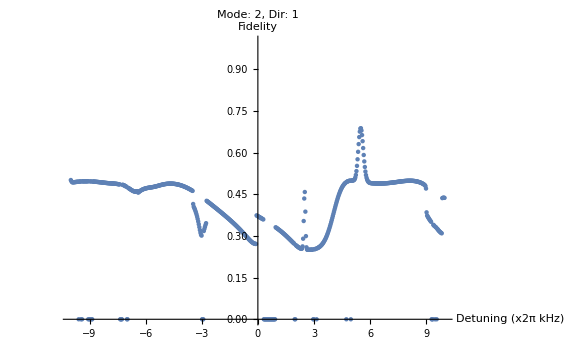

```mathematica
{Max[usweepres[[;;,1]]],#,Chop[(uArr[[#]]-wmvals[[dirDJ,modeDJ]])/wkhz]}&[First@Ordering[usweepres[[;;,1]],-1]]
usweepres[[%[[2]],2]]/wkhz
ListPlot[usweepres[[;;,1]],DataRange->(uArr[[{1,-1}]]-wmvals[[dirDJ,modeDJ]])/wkhz,PlotRange->{0,1},ImageSize->Large,AxesLabel->{"Detuning (x2π kHz)","Fidelity"},PlotLabel->"Mode: "<>ToString[modeDJ]<>", Dir: "<>ToString[dirDJ]]
```

## 2 Sosnova - RDX

## 2.1

### 2.1.1